# This is the Copy-Paste File!

## I’ll continue to add to this file as the semester goes on, so check back when you’re looking for something new.

## Line in 3D

```mathematica
ParametricPlot3D[{2+3t,1-t,-1+2t},{t,-5,5},Boxed->False,AxesLabel->{x,y,z},AxesOrigin->{0,0,0},PlotStyle->{Blue,Thick}]
```

## Plane using ContourPlot3D

```mathematica
ContourPlot3D[3x+y+2z==6,{x,-10,10},{y,-10,10},{z,-10,10},AxesLabel->{x,y,z},AxesOrigin->{0,0,0},Boxed->False,Mesh->{10,10,10},ContourStyle->Directive[Blue,Opacity[0.5]]]
```

-Graphics3D-

## Plane using Plot3D

```mathematica
Plot3D[(6-3x-y)/2,{x,-10,10},{y,-10,10},Boxed->False,AxesOrigin->{0,0,0},Mesh->{10,10},PlotStyle->{Blue,Opacity[0.5]}]
```

-Graphics3D-

## Point in 2D

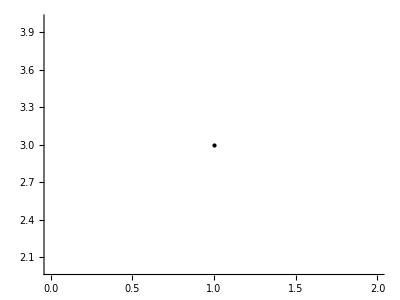

```mathematica
Graphics[{PointSize[Large],Point[{1,3}]},Axes->True]
```

## Point in 3D

```mathematica
Graphics3D[{PointSize[Large],Point[{2,0,0}]},AxesLabel->{x,y,z},AxesOrigin->{0,0,0},Boxed->False,Axes->True]
```

-Graphics3D-

## Vector in 2D

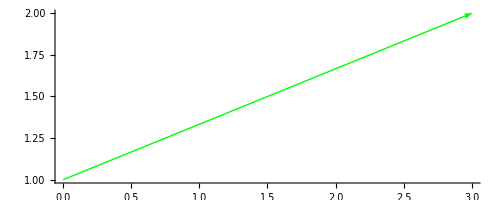

```mathematica
Graphics[{Green,Thick,Arrow[{{0,1},{3,2}}]},Axes->True]
```

## Vector in 3D

```mathematica
Graphics3D[{Red,Thick,Arrow[{{0,0,0},{3,1,2}}]},Boxed->False,Axes->True,AxesLabel->{x,y,z},AxesOrigin->{0,0,0}]
```

-Graphics3D-

## Vector Projection

```mathematica
Projection[{3,1,2},{5,4,6}]
```

{155/77,124/77,186/77}

## Cross Product

```mathematica
Cross[{1,2,3},{3,2,1}]
```

{-4,8,-4}

## Dot Product

```mathematica
Dot[{1,2,3},{3,2,1}]
```

10

## Surface using ContourPlot3D

```mathematica
ContourPlot3D[z==x^2+3y^2,{x,-5,5},{y,-5,5},{z,-5,5},AxesLabel->{x,y,z},AxesOrigin->{0,0,0},Boxed->False,Mesh->{5,5,5},MeshStyle->Thick,ContourStyle->Directive[Purple,Opacity[0.5]]]
```

-Graphics3D-

## Parametric Curve in 2D

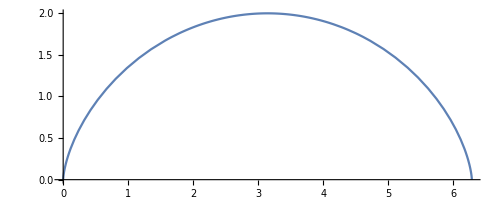

```mathematica
ParametricPlot[{t-Sin[t],1-Cos[t]},{t,0,2*Pi}]
```

## Function in 2D

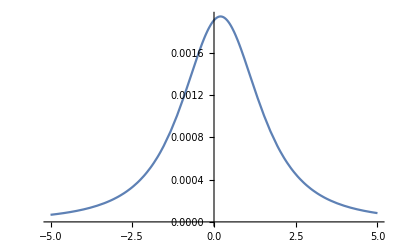

```mathematica
Plot[(65-8x+20x^2)^(-3/2),{x,-5,5}]
```

## Curve in 3D

```mathematica
ParametricPlot3D[{1-Cos[2t],t+Sin[t],t^2},{t,-Pi,Pi},Boxed->False,AxesLabel->{x,y,z},AxesOrigin->{0,0,0},PlotStyle->{Blue,Thick}]
```

-Graphics3D-

## Curvature

```mathematica
ArcCurvature[{2Sin[t],t,2Cos[t]},t]//Simplify
```

2/5

## Contour Map

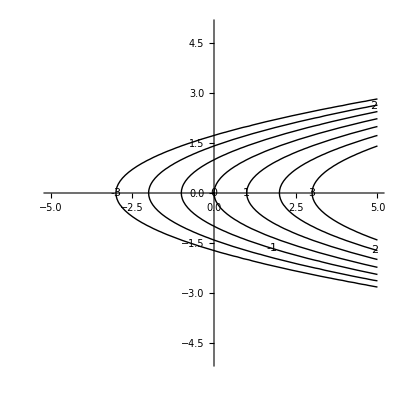

```mathematica
ContourPlot[x-y^2,{x,-5,5},{y,-5,5},Contours->{-3,-2,-1,0,1,2,3},ContourShading->None,ContourLabels->True,Frame->False,Axes->True,AxesOrigin->{0,0}]
```

## Function using Plot3D

```mathematica
Plot3D[Sqrt[6-3x+y]/(x+4),{x,-10,10},{y,-10,10},AxesLabel->{x,y,z},AxesOrigin->{0,0,0},Boxed->False,PlotStyle->{Blue,Opacity[0.5]}]
```

-Graphics3D-

## Contour Plot showing Level Surfaces of a Three-Variable Function

```mathematica
ContourPlot3D[x^2+y^2+z^2,{x,-10,10},{y,-10,10},{z,-10,10},Contours->10,AxesOrigin->{0,0,0},Boxed->False]
```

-Graphics3D-

## Partial Derivatives

### First-Order Partial Derivatives

```mathematica
D[9-2x+4y-x^2-4y^2,x]
```

-2-2 x

```mathematica
D[9-2x+4y-x^2-4y^2,y]
```

4-8 y

### Second-Order Partial Derivatives

```mathematica
D[9-2x+4y-x^2-4y^2,{x,2}]
```

-2

```mathematica
D[9-2x+4y-x^2-4y^2,{y,2}]
```

-8

```mathematica
D[9-2x+4y-x^2-4y^2,x,y]
```

0

## The Gradient

```mathematica
Grad[9-2x+4y-x^2-4y^2,{x,y}]
```

{-2-2 x,4-8 y}

## Critical Points

### Use NSolve if Solve does not work.

```mathematica
Solve[{D[9-2x+4y-x^2-4y^2,x]==0,D[9-2x+4y-x^2-4y^2,y]==0},{x,y}]
```

{{x→-1,y→1/2}}

## The Discriminant

```mathematica
Det[{{D[9-2x+4y-x^2-4y^2,{x,2}],D[9-2x+4y-x^2-4y^2,x,y]},{D[9-2x+4y-x^2-4y^2,x,y],D[9-2x+4y-x^2-4y^2,{y,2}]}}]
```

16

## Region Plot (in 2D)

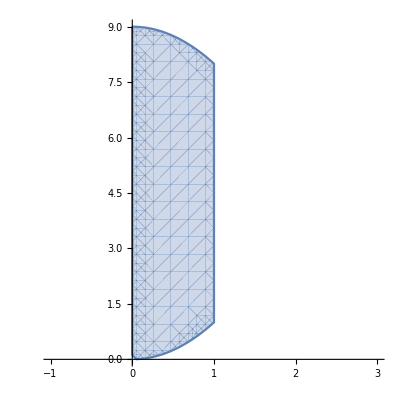

```mathematica
RegionPlot[{x^2<=y<=9-x^2&&0<=x<=1},{x,-1,3},{y,0,9},Frame->False,Axes->True]
```

## RegionPlot3D

```mathematica
RegionPlot3D[(1/4)*(3-x-y)<=z<=3-x-y,{x,0,3},{y,0,3},{z,0,3},Boxed->False,AxesOrigin->{0,0,0},Mesh->None,PlotStyle->Directive[Blue,Opacity[0.3]]]
```

-Graphics3D-

## Double Integral

```mathematica
Integrate[4*y^2,{x,0,7},{y,0,14-2x}]
```

19208/3

## Triple Integral

```mathematica
Integrate[x*y,{x,0,1},{y,0,1-x},{z,0,1-x-y}]
```

1/120

## Some fancy plotting

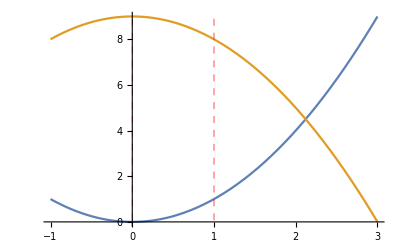

```mathematica
Plot[{x^2,9-x^2},{x,-1,3},GridLines->{{0,1},{}},GridLinesStyle->Directive[Red,Thick,Dashed]]
```

## Polygons

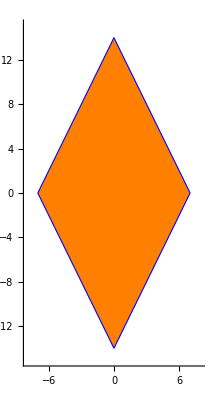

```mathematica
Graphics[{FaceForm[Orange],EdgeForm[Directive[Thick,Blue]],Polygon[{{-7,0},{0,-14},{7,0},{0,14}}]},Axes->True,PlotRange->{{-8,8},{-15,15}}]
```